### Подгружаем данные

В первом датасете каждая строка представляет собой встречу (в пределах 50 м) между двумя пользователями. Первый столбец - шаг по времени в виде целого числа. В столбцах 2 и 3 указаны идентификационные номера пользователей. В столбце 4 указано расстояние между пользователями на данном временном шаге, округленное до ближайшего метра.

```mathematica
KisslerDataS1=Import["https://raw.githubusercontent.com/skissler/haslemere/master/Kissler_DataS1.csv"];
(*KisslerDataS1=Import[FileNameJoin[{NotebookDirectory[],"Kissler_DataS1.csv"}],"CSV"];*)
```

Соответствие шага по времени из первого столбца между индексами времени в реальное время по британскому стандартному времени (BST).

```mathematica
KisslerDataS2=Import["https://raw.githubusercontent.com/skissler/haslemere/master/Kissler_DataS2.csv"];
(*KisslerDataS2=Import[FileNameJoin[{NotebookDirectory[],"Kissler_DataS2.csv"}],"CSV"];*)
```

### Обрабатываем данные

#### Данные наблюдений разделены на три дня. Зафиксируем временные отсечки для каждого дня.

```mathematica
temcut={{1,192},{193,384},{385,576}};
```

#### Приводим KisslerDataS1 к виду {{{1,...,...,...},{1,...,...,...},...},{{2,...,...,...},{2,...,...,...},...},...,{{576,...,...,...},{576,...,...,...},...}} получая таким образом последовательность из списков где каждый список представляет собой состояние сети в определенный момент времени.

```mathematica
datasep=Table[Cases[KisslerDataS1,{i,_,_,_}],{i,1,temcut⟦3,2⟧}];
```

#### Копия сети где отброшены все ребра с расстоянием более 5 метров.

```mathematica
datasep5m=Table[Cases[datasep⟦i⟧,{_,_,_,x_Integer}/;x≤5],{i,1,Length[datasep]}];
```

#### Создаем для каждого временного состояния список ребер.

```mathematica
edgelist=Table[Table[datasep⟦j,i,2⟧<->datasep⟦j,i,3⟧,{i,1,Length[datasep⟦j⟧]}],{j,1,Length[datasep]}];
```

```mathematica
edgelist5m=Table[Table[datasep5m⟦j,i,2⟧<->datasep5m⟦j,i,3⟧,{i,1,Length[datasep5m⟦j⟧]}],{j,1,Length[datasep5m]}];
```

#### В исследуемой сети у всех ребер есть расстояния.

```mathematica
edgelength=Table[Table[N[datasep⟦j,i,4⟧],{i,1,Length[datasep⟦j⟧]}],{j,1,Length[datasep]}];
```

```mathematica
edgelength5m=Table[Table[N[datasep5m⟦j,i,4⟧],{i,1,Length[datasep5m⟦j⟧]}],{j,1,Length[datasep5m]}];
```

#### Предполагая, что вероятность заражения падает экспоненциально с расстоянием, введем коэффициент равный обратной экспоненте от расстояния.

```mathematica
w=ⅇ^-edgelength;
```

```mathematica
w5m=ⅇ^-edgelength5m;
```

#### Функция объединения сети в более широкие временные рамки.

Входные данные: список ребер, веса ребер, первая временная отсечка, последняя временная отсечка, количество временных шагов, которое мы объединяем в один шаг. Выходные данные: список ребер, веса ребер.

```mathematica
NetUnion[el_,we_,tstart_,tend_,tstep_]:=Module[{data=Table[Normal[GroupBy[{Flatten[el⟦i;;i+tstep-1⟧],Flatten[we⟦i;;i+tstep-1⟧]}ᵀ,First]]⟦All,2⟧,{i,1,tend-tstep+1,3}]},data=Table[{DeleteDuplicates[Flatten[data⟦i,All,All,1⟧]],Total[data⟦i,All,All,2⟧,{-1}]/tstep},{i,1,(tend-tstart+1)/tstep}];data]
```

#### Шаг в 15 минут

```mathematica
nu15min=NetUnion[edgelist,w,1,576,3];
```

```mathematica
nu15min5m=NetUnion[edgelist5m,w5m,1,576,3];
```

```mathematica
timedata15min=Table[KisslerDataS2⟦i,2⟧,{i,1,576,3}];
```

#### Шаг в 30 минут

```mathematica
nu30min=NetUnion[edgelist,w,1,576,6];
```

```mathematica
nu30min5m=NetUnion[edgelist5m,w5m,1,576,6];
```

```mathematica
timedata30min=Table[KisslerDataS2⟦i,2⟧,{i,1,576,6}];
```

#### Шаг в 1 час

```mathematica
nu1h=NetUnion[edgelist,w,1,576,12];
```

```mathematica
nu1h5m=NetUnion[edgelist5m,w5m,1,576,12];
```

```mathematica
timedata1h=Table[KisslerDataS2⟦i,2⟧,{i,1,576,12}];
```

#### Шаг в 4 часа

```mathematica
nu4h=NetUnion[edgelist,w,1,576,48];
```

```mathematica
nu4h5m=NetUnion[edgelist5m,w5m,1,576,48];
```

```mathematica
timedata4h=Table[KisslerDataS2⟦i,2⟧,{i,1,576,48}];
```

#### Шаг в 16 часов (1 день наблюдений)

```mathematica
nu1d=NetUnion[edgelist,w,1,576,192];
```

```mathematica
nu1d5m=NetUnion[edgelist5m,w5m,1,576,192];
```

```mathematica
timedata1d={"Thu 12 Oct 2017","Fri 13 Oct 2017", "Sat 14 Oct 2017"};
```

#### Объединенная сеть

```mathematica
nuall=NetUnion[edgelist,w,1,576,576];
```

```mathematica
edgelistnu=nuall⟦1,1⟧;
```

```mathematica
wnu=nuall⟦1,2⟧;
```

```mathematica
nuall5m=NetUnion[edgelist5m,w5m,1,576,576];
```

```mathematica
edgelistnu5m=nuall5m⟦1,1⟧;
```

```mathematica
wnu5m=nuall5m⟦1,2⟧;
```

#### Подсчитаем количество уникальных вершин в сети за всё время наблюдений.

```mathematica
vertexcount=VertexCount[Graph[edgelistnu]];
```

```mathematica
vertexcount5m=VertexCount[Graph[edgelistnu5m]];
```

#### Создадим сетку с вершинами.

```mathematica
grid=Partition[Flatten[Table[{i,j},{i,1,Ceiling[√vertexcount]},{j,1,Ceiling[√vertexcount]}]],2]⟦1;;vertexcount⟧;
```

#### Координаты вершин полученные силовым методом укладки графа.

```mathematica
altgrid=Module[{g=Graph[edgelistnu,GraphLayout->"SpringElectricalEmbedding"]},SortBy[{VertexList[g],AnnotationValue[{g,#},VertexCoordinates]&/@VertexList[g]}ᵀ,First]];
```

```mathematica
altgrid5m=Module[{g=Graph[edgelistnu5m,GraphLayout->"SpringElectricalEmbedding"]},SortBy[{VertexList[g],AnnotationValue[{g,#},VertexCoordinates]&/@VertexList[g]}ᵀ,First]];
```

### Визуализация сети в виде квадратной решетки

#### За всё время

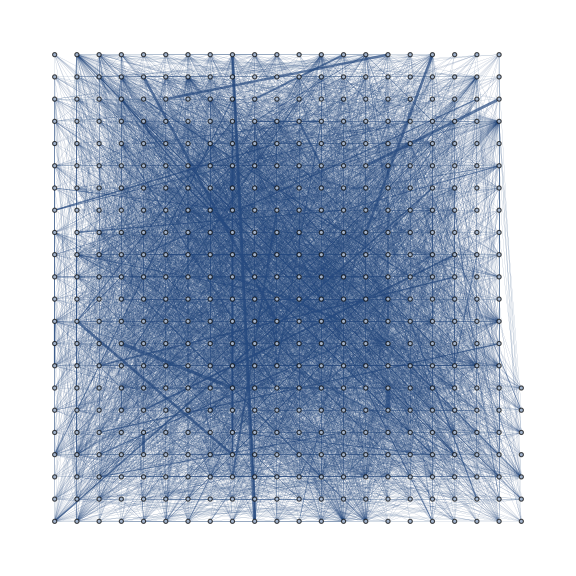

```mathematica
EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelistnu,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[edgelistnu⟦i⟧->Thickness[0.01wnu⟦i⟧],{i,1,Length[edgelistnu]}],ImageSize->Large]
```

#### За всё время (отсечка в 5м)

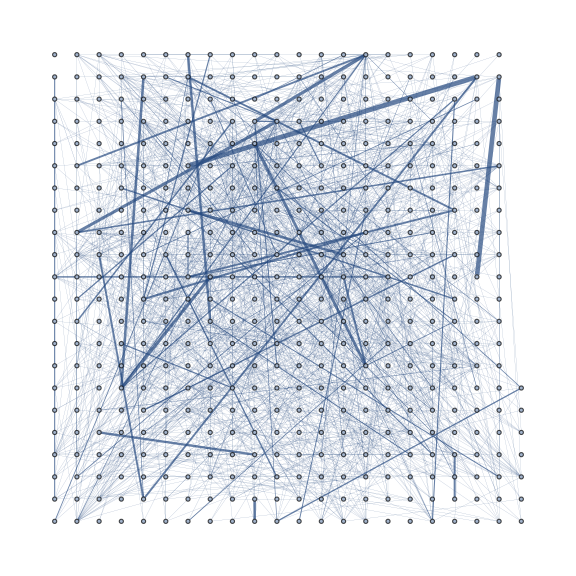

```mathematica
EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelistnu5m,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[edgelistnu5m⟦i⟧->Thickness[0.01wnu⟦i⟧],{i,1,Length[edgelistnu5m]}],ImageSize->Large]
```

#### По дням

```mathematica
v1d=Table[Grid[{{timedata1d⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu1d⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu1d⟦j,1,i⟧->Thickness[0.01nu1d⟦j,2,i⟧],{i,1,Length[nu1d⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu1d]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1d.gif"}],v1d];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1d.m"}],v1d];
```

#### По дням (отсечка в 5м)

```mathematica
v1d5m=Table[Grid[{{timedata1d⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu1d5m⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu1d5m⟦j,1,i⟧->Thickness[0.01nu1d5m⟦j,2,i⟧],{i,1,Length[nu1d5m⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu1d5m]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1d5m.gif"}],v1d5m];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1d5m.m"}],v1d5m];
```

#### Раз в 4 часа

```mathematica
v4h=Table[Grid[{{timedata4h⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu4h⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu4h⟦j,1,i⟧->Thickness[0.01nu4h⟦j,2,i⟧],{i,1,Length[nu4h⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu4h]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v4h.gif"}],v4h];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v4h.m"}],v4h];
```

#### Раз в 4 часа (отсечка в 5м)

```mathematica
v4h5m=Table[Grid[{{timedata4h⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu4h5m⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu4h5m⟦j,1,i⟧->Thickness[0.01nu4h5m⟦j,2,i⟧],{i,1,Length[nu4h5m⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu4h5m]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v4h5m.gif"}],v4h5m];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v4h5m.m"}],v4h5m];
```

#### Раз в 1 час

```mathematica
v1h=Table[Grid[{{timedata1h⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu1h⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu1h⟦j,1,i⟧->Thickness[0.01nu1h⟦j,2,i⟧],{i,1,Length[nu1h⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu1h]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1h.gif"}],v1h];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1h.m"}],v1h];
```

#### Раз в 1 час (отсечка в 5м)

```mathematica
v1h5m=Table[Grid[{{timedata1h⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu1h5m⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu1h5m⟦j,1,i⟧->Thickness[0.01nu1h5m⟦j,2,i⟧],{i,1,Length[nu1h5m⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu1h5m]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1h5m.gif"}],v1h5m];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v1h5m.m"}],v1h5m];
```

#### Раз в 30 минут

```mathematica
v30min=Table[Grid[{{timedata30min⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu30min⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu30min⟦j,1,i⟧->Thickness[0.01nu30min⟦j,2,i⟧],{i,1,Length[nu30min⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu30min]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v30min.gif"}],v30min];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v30min.m"}],v30min];
```

#### Раз в 30 минут (отсечка в 5м)

```mathematica
v30min5m=Table[Grid[{{timedata30min⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu30min5m⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu30min5m⟦j,1,i⟧->Thickness[0.01nu30min5m⟦j,2,i⟧],{i,1,Length[nu30min5m⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu30min5m]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v30min5m.gif"}],v30min5m];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v30min5m.m"}],v30min5m];
```

#### Раз в 15 минут

```mathematica
v15min=Table[Grid[{{timedata15min⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu15min⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu15min⟦j,1,i⟧->Thickness[0.01nu15min⟦j,2,i⟧],{i,1,Length[nu15min⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu15min]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v15min.gif"}],v15min];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v15min.m"}],v15min];
```

#### Раз в 15 минут (отсечка в 5м)

```mathematica
v15min5m=Table[Grid[{{timedata15min⟦j⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],nu15min5m⟦j,1⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[nu15min5m⟦j,1,i⟧->Thickness[0.01nu15min5m⟦j,2,i⟧],{i,1,Length[nu15min5m⟦j,1⟧]}],ImageSize->Large]}}],{j,1,Length[nu15min5m]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v15min5m.gif"}],v15min5m];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v15min5m.m"}],v15min5m];
```

#### Раз в 5 минут

```mathematica
v5min=Table[Grid[{{KisslerDataS2⟦j,2⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelist⟦j⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[edgelist⟦j,i⟧->Thickness[0.01w⟦j,i⟧],{i,1,Length[edgelist⟦j⟧]}],ImageSize->Large]}}],{j,1,Length[edgelist]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v5min.gif"}],v5min];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v5min.m"}],v5min];
```

#### Раз в 5 минут (отсечка в 5м)

```mathematica
v5min5m=Table[Grid[{{KisslerDataS2⟦j,2⟧},{EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelist5m⟦j⟧,VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],EdgeStyle->Table[edgelist5m⟦j,i⟧->Thickness[0.01w5m⟦j,i⟧],{i,1,Length[edgelist5m⟦j⟧]}],ImageSize->Large]}}],{j,1,Length[edgelist5m]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v5min5m.gif"}],v5min5m];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"v5min5m.m"}],v5min5m];
```

### Исследование характеристик сети

```mathematica
CCDF[arr_,nbins_]:=Table[N[{i,SurvivalFunction[EmpiricalDistribution[arr],i]}],{i,Min[arr],Max[arr],(Max[arr]-Min[arr])/(nbins-1)}]
```

```mathematica
DegCoef[g_]:=Abs[Normal[LinearModelFit[Evaluate[Log[CCDF[VertexDegree[g],100]]⟦2;;-2⟧],x,x]]⟦2,1⟧]
```

```mathematica
SF[arr_,n_]:=Flatten[Table[arr⟦j⟧,{j,1,Length[arr]},{i,1,n}]]
```

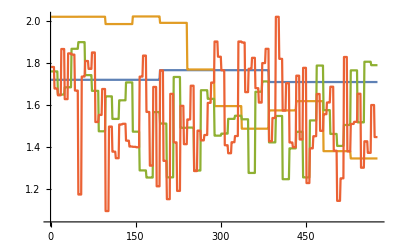

```mathematica
ListLinePlot[{SF[Table[DegCoef[v1d⟦j,1,2,1⟧],{j,1,Length[v1d]}],192],SF[Table[DegCoef[v4h⟦j,1,2,1⟧],{j,1,Length[v4h]}],48],SF[Table[DegCoef[v1h⟦j,1,2,1⟧],{j,1,Length[v1h]}],12],SF[Table[DegCoef[v30min⟦j,1,2,1⟧],{j,1,Length[v30min]}],6]}]
```